# 第2章 初等函数运算

## 2.1 多项式运算

### 1. 多项式基本运算

多项式的基本代数运算有加法、减法、乘法、除法、模运算

```mathematica
t1=x^2-2x-3;t2=x-3;
t1+t2
t1-t2
t1*t2
t1/t2
```

-6-x+x^2

-3 x+x^2

(-3+x) (-3-2 x+x^2)

(-3-2 x+x^2)/(-3+x)

给定两个单变量多项式a (x) 和b (x)，存在唯一的多项式q (x) 和r (x) 使得a (x) = b (x) q (x) + r (x)

"PolynomialQuotient[a(x),b(x),x]" | "两个多项式相除的商式"
"PolynomialRemainder[a(x),b(x),x]" | "两个多项式相除的余式"
"PolynomialQuotientRemainder[a(x),b(x),x]" | "同时给出两个多项式相除的商式和余式"

```mathematica
PolynomialQuotient[x^3+y^3,x-y,x]
PolynomialRemainder[x^3+y^3,x-y,x]
PolynomialQuotientRemainder[x^3+y^3,x-y,x]
```

x^2+x y+y^2

2 y^3

{x^2+x y+y^2,2 y^3}

### 2. 多项式元素提取

"PolynomialQ[expr,x]
PolynomialQ[expr,{x,y,...}]" | "检验expr是否关于变元x,y,...的多项式"
"Variables[poly]" | "多项式poly的变元列表"
"Exponent[poly,x]" | "poly中x的最大指数"
"Coefficient[poly,expr]" | "poly 中expr 的系数"
"Coefficient[poly,expr,n]" | "poly 中expr^n 的系数"
"Coefficient[poly，expr，0]" | "poly 中expr 与无关的项"
"CoefficientList[poly，{x1,x2,...}]" | "生成一个 poly中x1,x2,…的系数的数组"
"MonomialList[poly]" | "给出所有单项式的列表"

```mathematica
PolynomialQ[x^2-y^2,{x,y}]
```

True

```mathematica
PolynomialQ[x^2+x+2/y,{x,y}]
```

False

```mathematica
PolynomialQ[x^2+x+2/y,x]
```

True

```mathematica
poly1=(x-1)^(15);poly2=x^4+5 x^3 y^2-3 x y+6 y^4;
Variables[poly2]
```

{x,y}

```mathematica
Coefficient[poly1,x,5]
CoefficientList[poly2,x]
```

3003

{6 y^4,-3 y,0,5 y^2,1}

```mathematica
Coefficient[(x+y+z)^6,x^2*y*z^3]
```

60

### 3. 多项式展开与合并

"Expand[poly]" | "展开乘积和幂"
"Factor[poly]" | "完全因式分解"
"FactorTerms[poly]" | "提取数值因式"
"Collect[poly,x]" | "将多项式排列成x的幂的和的形式"
"Collect[poly,{x,y,...}]" | " 将多项式排列成x,y,.85 的幂的和的形式"

```mathematica
p1=(1+x^2)^3(4x-2)^2;
t1=Expand[p1]
```

4-16 x+28 x^2-48 x^3+60 x^4-48 x^5+52 x^6-16 x^7+16 x^8

```mathematica
p2=(1+2x+3y)^4;
t2=Expand[p2]
```

1+8 x+24 x^2+32 x^3+16 x^4+12 y+72 x y+144 x^2 y+96 x^3 y+54 y^2+216 x y^2+216 x^2 y^2+108 y^3+216 x y^3+81 y^4

```mathematica
Collect[t2,y]
```

1+8 x+24 x^2+32 x^3+16 x^4+(12+72 x+144 x^2+96 x^3) y+(54+216 x+216 x^2) y^2+(108+216 x) y^3+81 y^4

```mathematica
p3=(1+x+2y+3z)^2
Collect[Expand[p3],{x,y}]
```

(1+x+2 y+3 z)^2

1+x^2+4 y^2+6 z+9 z^2+x (2+4 y+6 z)+y (4+12 z)

```mathematica
Factor[t1]
```

4 (-1+2 x)^2 (1+x^2)^3

```mathematica
Factor[x^2-  x-1/2]
```

1/2 (-1-2 x+2 x^2)

```mathematica
Factor[x^2-  x-1/2,Extension->Sqrt[3]]
```

-1/4 (1+√3-2 x) (-1+√3+2 x)

```mathematica
Factor[x^8-41x^4+400,GaussianIntegers->True]
```

(-2+x) (-2 ⅈ+x) (2 ⅈ+x) (2+x) (-5+x^2) (5+x^2)

```mathematica
Factor[x^8-41x^4+400,Extension->{I,Sqrt[5]}]
```

-(√5-x) (√5-ⅈ x) (√5+ⅈ x) (-2+x) (-2 ⅈ+x) (2 ⅈ+x) (2+x) (√5+x)

```mathematica
FactorTerms[t1]
```

4 (1-4 x+7 x^2-12 x^3+15 x^4-12 x^5+13 x^6-4 x^7+4 x^8)

#### 有控制地展开，合并

"Expand[poly,patt]" | "展开poly,保持其中不与patt匹配的部分不变"
"PowerExpand[expr]" | "展 开 expr 中 的(ab)^c 和(a^b)^c"
"Collect[poly,patt]" | "将涉及与patt匹配的每个对象的分散的项合并起来"

```mathematica
Expand[(x+l)^2(y+1)^2,x]
```

l^2 (1+y)^2+2 l x (1+y)^2+x^2 (1+y)^2

```mathematica
Expand[(a[1]+a[2]+1)^2(b[1]+b[2]+1)^2,b[_]]
```

(1+a[1]+a[2])^2+2 (1+a[1]+a[2])^2 b[1]+(1+a[1]+a[2])^2 b[1]^2+2 (1+a[1]+a[2])^2 b[2]+2 (1+a[1]+a[2])^2 b[1] b[2]+(1+a[1]+a[2])^2 b[2]^2

除了c为整数，Mathematica 并不自动展开形如 (ab)^c 的表达式.一般，仅当a 和b 是正实数时，这样的展开才是正确的.然而，函数 PowerExpand 有效地假定a 和b 是正实数，并进行这样的展开

```mathematica
Expand[(x y)^n]
```

(x y)^n

```mathematica
PowerExpand[(x y)^n]
```

x^n y^n

```mathematica
PowerExpand[Log[x^n y^n]]
```

n Log[x]+n Log[y]

```mathematica
Expand[Log[x^n y^n]]
```

Log[x^n y^n]

```mathematica
t=a[1] x^2+a[2] y^2+2 a[1] x y+a[2]+a[3]
Collect[t,a[_]]
```

x^2 a[1]+2 x y a[1]+a[2]+y^2 a[2]+a[3]

(x^2+2 x y) a[1]+(1+y^2) a[2]+a[3]

### 4. 有理式的运算

"ExpandNumerator[expr]" | "仅展开分子"
"ExpandDenominator[expr]" | "展开表达式expr中的分式的分母"
"Expand[expr]" | "展开分子，每一项除以分母"
"ExpandAll[expr]" | "完全展开分子和分母"
"ExpandAll[expr,patt]" | "避免展开不含与patt匹配的项的部分"

```mathematica
t=(1-x)/((x+1)^2)+(x+1)2/(x (1-x));
ExpandDenominator[t]
```

(2 (1+x))/(x-x^2)+(1-x)/(1+2 x+x^2)

```mathematica
ExpandNumerator[t]
```

(1-x)/(1+x)^2+(2+2 x)/((1-x) x)

```mathematica
ExpandAll[(x+1)^2/(y+2)^3+(z+1)^2/(z-3)^2,z]
```

(1+x)^2/(2+y)^3+1/(9-6 z+z^2)+(2 z)/(9-6 z+z^2)+z^2/(9-6 z+z^2)

"Together[expr]" | "对所有项进行通分"
"Apart[expr]" | "将表达式写为具有最简分母的项的和"
"Cancel[expr]" | "约去分子分母的公因式"
"Factor[expr]" | "进行完全因式分解"

```mathematica
u=(4x+x^2)/(-x+x^2)+(x^2+3x+2)/(x^2+1);
Together[u]
Factor[u]
```

(2 (1+3 x^2+x^3))/((-1+x) (1+x^2))

(2 (1+3 x^2+x^3))/((-1+x) (1+x^2))

```mathematica
Cancel[(x^2+5x+6)/(x^2+3x+2)]
```

(3+x)/(1+x)

```mathematica
Cancel[(x^2+2 √2 x+2)/(x^2-2)]
```

(2+2 √2 x+x^2)/(-2+x^2)

```mathematica
Cancel[(x^2+2 √2 x+2)/(x^2-2),Extension->Automatic]
```

(-√2-x)/(√2-x)

```mathematica
Apart[(x^2+5x)/(x^4+x^3-x-1)]
```

1/(-1+x)+2/(1+x)+(-1-3 x)/(1+x+x^2)

#### 5. 化简

"Simplify[expr]" | "简化表达式"
"Simplify[expr,assum]" | "依据假设条件assum化简表达式"
"FullSimplify[expr]" | "尝试用更广泛的变换化简"
"FullSimplify[expr,assum]" | "依据假设条件assum深入化简表达式"
"Assuming[assum,expr]" | "依据假设条件assum执行表达式"

```mathematica
Simplify[(1-x)/(1-x^2)]
```

1/(1+x)

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
Simplify[1/Sqrt[x]-Sqrt[1/x]]
```

-√(1/x)+1/(√x)

```mathematica
Simplify[1/Sqrt[x]-Sqrt[1/x],x>0]
```

0

```mathematica
Simplify[(x+y)/2≥Sqrt[x y],x≥0&&y≥0]
```

True

```mathematica
Simplify[Sin[n Pi],n∈Integers]
```

0

```mathematica
Simplify[Sin[n Pi]]
```

Sin[n π]

### 6. 多项式组的运算

"PolynomialQuotient[poly1,poly2,x]" | "求多项式poly1除以poly2 的结果，去掉余项"
"PolynomialRemainder[poly1,poly2,x]" | "求 x 的多项式poly1 除以poly2 的余项"
"PolynomialGCD[poly1,poly2]" | "求两个多项式的最大公因式"
"PolynomialLCM[poly1,poly2]" | "求两个多项式的最小公倍式"

```mathematica
PolynomialRemainder[x^2,x+1,x]
```

1

```mathematica
PolynomialQuotient[x^2,x+1,x]
```

-1+x

```mathematica
PolynomialGCD[(1-x)^2 (1+x) (2+x),(l-x) (2+x)(3+x)]
```

2+x

## 2.2 三角函数运算

"TrigExpand[expr]" | "将三角函数式展开成Sin[x],Cos[x] 的表达式"
"TrigFactor[expr]" | "将三角函数分解因式成为项的积"
"TrigFactorList[expr]" | "给出各项及其指数的列表"
"TrigReduce[expr]" | "用三角恒等式等化简"
"TrigToExp[expr]" | "用指数函数表示三角函数"
"ExpToTrig[expr]" | "用三角函数表示指数函数 "

```mathematica
?Trig*
```

```mathematica
TrigExpand[Sin[ x/2]Cos[2 y]]
```

Cos[y]^2 Sin[x/2]-Sin[x/2] Sin[y]^2

```mathematica
Expand[Sin[2 x]Cos[2 y],Trig->True]
```

2 Cos[x] Cos[y]^2 Sin[x]-2 Cos[x] Sin[x] Sin[y]^2

```mathematica
TrigFactor[Sin[2 x]Cos[2 y]]
```

4 Cos[x] Sin[x] Sin[π/4-y] Sin[π/4+y]

```mathematica
TrigReduce[Sin[2 x]Cos[2 y]]
```

1/2 (Sin[2 x-2 y]+Sin[2 x+2 y])

对双曲函数也能进行运算.

```mathematica
TrigExpand[Tanh[x+y]]
```

(Cosh[y] Sinh[x])/(Cosh[x] Cosh[y]+Sinh[x] Sinh[y])+(Cosh[x] Sinh[y])/(Cosh[x] Cosh[y]+Sinh[x] Sinh[y])

```mathematica
Sin[x]^2/Cos[x]
TrigFactorList[%]
```

Sin[x] Tan[x]

{{1,1},{Sin[x],2},{Cos[x],-1}}

```mathematica
TrigToExp[Tan[x]]
```

(ⅈ (ⅇ^(-ⅈ x)-ⅇ^(ⅈ x)))/(ⅇ^(-ⅈ x)+ⅇ^(ⅈ x))

```mathematica
ExpToTrig[Exp[x]-Exp[-x]]
```

2 Sinh[x]

## 2.3 方程运算

### 1 方程的表示

方程通常表示为:      ”lhs==rhs”------逻辑表达式.

方程组通常表示为      ￿{eqn1,eqn2,...}  ￿或￿eqn1 && eqn2 && .

将方程中的等号”==”换成不等号”<”, “>”,”<=”,  “>=”, “!=”就得到不等式.

方程和不等式也可以被展开、合并、或化简

```mathematica
eqn=(1-x)(1+y)==(1+x)(1-y);Expand[eqn]
```

1-x+y-x y==1+x-y-x y

```mathematica
Collect[eqn,x]
```

1+y-x (1+y)==1+x (1-y)-y

对于逻辑结构比较复杂的方程或不等式 “LogicalExpand[expr]”将逻辑表
      达式expr 展开为  “expr1||expr2||...”    的形式.  其中 ||   表示逻辑“ 或” 运算

```mathematica
eqn=(x+y>2||x-y<1)&&(x+y<1||x-y>2);
LogicalExpand[eqn]
```

(x-y>2&&x+y>2)||(x-y>2&&x-y<1)||(x+y>2&&x+y<1)||(x-y<1&&x+y<1)

Eliminate[eqns,vars]          将方程组eqns中的部分变元消去

```mathematica
p1=x^2+y^2+z^2-(a^2+b^2+c^2);p2=x+y+z-(a+b+c);
p3=a^2+b^2+c^2-2a+2b+1;p4=a+b-2c;
Eliminate[{p1,p2,p3,p4}=={0,0,0,0},{a,b,c}]
```

3 x^4+x (16 y+16 z)+x^2 (-10+6 y^2+6 z^2)==-3+10 y^2-3 y^4-16 y z+10 z^2-6 y^2 z^2-3 z^4

### 2 一般方程的求解

Solve[eqns,vars]   求方程（组）eqns的所有准确解vars
方程中只有一个未知量时，vars可不写。

```mathematica
Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

例题：求解方程组{2 x+3 y=7
3x+4y=10

```mathematica
Solve[2 x+3 y==7&&3 x+4 y==10, {x,y}]
```

{{x→2,y→1}}

```mathematica
Solve[{2 x+3 y==7,3 x+4 y==10},{x,y}]
```

{{x→2,y→1}}

说明：1.如果要利用方程的解代入表达式求值，可直接用取代运算符/.
            2.方程的解以列表形式给出，可以用Part提取列表元素.

例题： 求解方程组{x^2+y=4
2x-y=1, 并计算表达式√(x^2+y^2)在这些解上的值.

```mathematica
solution=Solve[{x^2+y==4, 2x-y==1},{x,y}]
```

{{x→-1-√6,y→-3-2 √6},{x→-1+√6,y→-3+2 √6}}

```mathematica
√(x^2+y^2)/.solution
```

{√((-3-2 √6)^2+(-1-√6)^2),√((-1+√6)^2+(-3+2 √6)^2)}

```mathematica
Simplify[%]
```

{√(40+14 √6),√(40-14 √6)}

例题：计算方程-735+1337 x-778 x^2+198 x^3-23 x^4+x^5=0所有根的平方和.

```mathematica
solution=Solve[-735+1337 x-778 x^2+198 x^3-23 x^4+x^5==0,x]
```

{{x→1},{x→3},{x→5},{x→7},{x→7}}

```mathematica
solution[[1]]
```

{x→1}

```mathematica
solution[[1,1]]
```

x→1

```mathematica
solution[[1,1,2]]
solution[[1,1,1]]
```

1

x

```mathematica
Sum[solution[[k,1,2]]^2,{k,1,5}]
Total[solution^2]
```

133

{(x→1)^2+(x→3)^2+(x→5)^2+2 (x→7)^2}

对三次或二次方程,Mathematica 总能给出解的显式公式，这些公式的一个重要特点是它们仅包含根式。然而，作为基本的数学事实， 五次及五次以上的方程，一般不再可能给出仅含根式的解的显式公式.虽然在一些特殊情形可以做到这一点， 但绝大多数情形是不行的

NSolve[eqns, vars]  求方程eqns的所有数值解vars

NSolve[eqns, vars,n]  
求方程eqns的所有数值解vars, 达到n位精度

```mathematica
NSolve[x^5==x+1,x]
```

{{x→-0.764884-0.352472 ⅈ},{x→-0.764884+0.352472 ⅈ},{x→0.181232-1.08395 ⅈ},{x→0.181232+1.08395 ⅈ},{x→1.1673}}

```mathematica
NSolve[x^5==x+1,x,20]
```

{{x→-0.76488443360058472603-0.3524715460317262493 ⅈ},{x→-0.76488443360058472603+0.3524715460317262493 ⅈ},{x→0.1812324444698753839-1.0839541013177106684 ⅈ},{x→0.1812324444698753839+1.0839541013177106684 ⅈ},{x→1.1673039782614186843}}

Roots[eqn, var]
求一元多项式方程eqn的所有准确解var

NRoots[eqn, var]
求一元多项式方程eqn的所有数值解var

Root[f,k]
求一元多项式f的第k个根

```mathematica
Roots[x^3-5x+4==0,x]
```

x==1/2 (-1-√17)||x==1/2 (-1+√17)||x==1

```mathematica
NRoots[x^5==x+1.0,x,20]
```

x==-0.7648844336005847-0.352471546031726 ⅈ||x==-0.7648844336005847+0.352471546031726 ⅈ||x==0.181232444469875-1.083954101317711 ⅈ||x==0.181232444469875+1.083954101317711 ⅈ||x==1.167303978261419

例：求出方程x^4 + x^3-8 x^2 - 5 x - 15 = 0 的所有大于 2 的解

```mathematica
solutions=Roots[x^4+x^3-8x^2-5x+15==0,x]
```

x==1/2 (-1-√13)||x==1/2 (-1+√13)||x==√5||x==-√5

```mathematica
solutions&&x>2//Simplify
```

x==√5

将形如 lhs= = rhs 的方程转换为形如 lhs->rhs 的变换规则

```mathematica
u=Roots[x^2+3 x==2,x]
```

x==1/2 (-3-√17)||x==1/2 (-3+√17)

```mathematica
{ToRules[u]}
```

{{x→1/2 (-3-√17)},{x→1/2 (-3+√17)}}

```mathematica
Clear[a]
```

```mathematica
x^2+ a x/.%
```

{1/4 (-3-√17)^2+1/2 (-3-√17) a,1/4 (-3+√17)^2+1/2 (-3+√17) a}

### 包含函数的方程求解

当方程能被化简为纯代数形式时， 能够使用 Solve 系统地求解该方程.但至少在缺省选项设置 InverseFunction- >True 下,Solve 也偿试处理一些其它类型的方程

```mathematica
Solve[ArcSin[x]==a,x]
```

{{x→ConditionalExpression[Sin[a],(Re[a]==-π/2&&Im[a]≥0)||-π/2<Re[a]<π/2||(Re[a]==π/2&&Im[a]≤0)]}}

大部分包含超越函数的方程不能精确求解.有些场合可以求出部分解，但也不能求出全部
解.

FindRoot[f,{x,a}]  以a为初值，求函数f(x)的一个根x

FindRoot[eqns,{x,a}]以a为初值，求方程eqns的一个解x

例题：求解方程 sin x =x^2-1

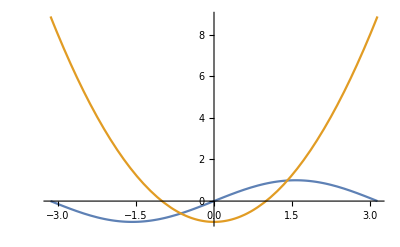

```mathematica
Plot[{Sin[x], x^2-1},{x,-Pi,Pi}]
```

```mathematica
FindRoot[Sin[x]==x^2-1, {x,-1}]
```

{x→-0.636733}

例题：求方程x*sin (x) = 1 在区间[-10，10] 上的解。

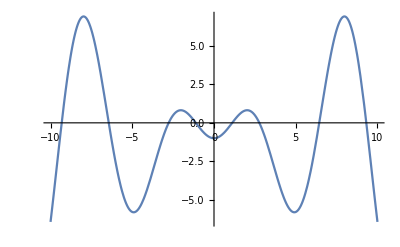

```mathematica
Plot[x*Sin[x]-1,{x,-10,10}]
```

```mathematica
a={-9,-6,-3,-1,1,3,6,9}
```

{-9,-6,-3,-1,1,3,6,9}

```mathematica
Table[FindRoot[x*Sin[x]==1,{x,a[[i]]}],{i,8}]
```

{{x→-9.31724},{x→-6.43912},{x→-2.7726},{x→-1.11416},{x→1.11416},{x→2.7726},{x→6.43912},{x→9.31724}}

例题： 求方程组{e^x+ln y=2
sin x+sin y=1的近似解.

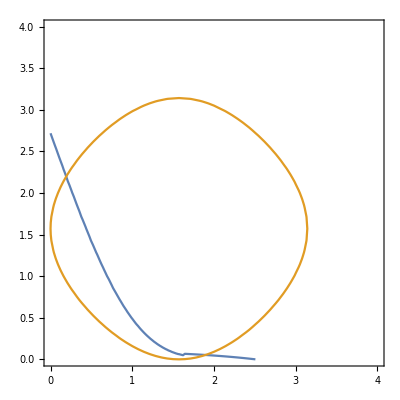

```mathematica
ContourPlot[{Exp[x]+Log[y]==2, Sin[x]+Sin[y]==1},{x,0,4},{y,0,4}]
```

```mathematica
sol1=FindRoot[{Exp[x]+Log[y]==2, Sin[x]+Sin[y]==1},{x,0.4},{y,2}]
```

{x→0.192202,y→2.19918}

Reduce[expr, vars, dom]  
 化简方程或不等式expr并求所有解vars

FindInstance[expr, vars, dom, n]
求方程或不等式expr的n个特解vars

```mathematica
Reduce[a*x^2+b*x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

Reduce 给出的结果是表示方程的所有可能解的逻辑语句,  弄清参数在什么值下解存在

```mathematica
Reduce[3x-2y>a&&x+y<b,{x,y}]
```

(a|b)∈ℝ&&((x≤1/5 (a+2 b)&&y<1/2 (-a+3 x))||(x>1/5 (a+2 b)&&y<b-x))

```mathematica
FindInstance[x^2+y^2==z^2&&0<x<y<z<20,{x,y,z},Integers,3]
```

{{x→3,y→4,z→5},{x→9,y→12,z→15},{x→5,y→12,z→13}}

### 3 递归方程的求解

RecurrenceTable[eqns, expr, nspec]
由递归关系eqns求表达式expr生成的数列

RSolve[eqns, a[n], n]
由递归关系eqns求数列an的通项公式

```mathematica
RecurrenceTable[{a[n+2]==a[n+1]+a[n],a[1]==a[2]==1},a[n],{n,10,20}]
```

{55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
RSolve[b[1+n]==1/3 (x* b[n]+y),b[n],n]
```

{{b[n]→-(3^-n (3^n-x^n) y)/(-3+x)+3^(1-n) x^(-1+n) C[1]}}

## 2.4 求和与乘积运算

### 1 求和

Sum[f,{i,m,n,d}]   
求和f(i)，其中i在区间[m,n]上以步长d变化

Sum[f,{i,list}]
求和f(i)，其中i为列表list中的元素

Sum[f,{i1,m1,n1,d1},{i2,m2,n2,d2},...]
多指标求和f(i1,i2,...)，其中i1为最外层循环指标

Sum[f,i]
形式求和，结果g满足g(i)-g(i-1)=f(i)

```mathematica
Sum[1/(n^3),{n,10}]		(* 计算∑_(n=1)^10 1/n^3 准确值*)
```

19164113947/16003008000

```mathematica
NSum[1/n^3,{n,10}]                 (* 计算∑_(n=1)^10 1/n^3 近似值*)
```

1.19753

```mathematica
N[Sum[1/(n^3),{n,10}],20]
```

1.1975319856741932517

```mathematica
Sum[1/n^2,{n,Infinity}]   (*Sum可无穷求和*)
```

π^2/6

```mathematica
Sum[i^2,{i,m,n}]      (*求和界限可以是变元*)
```

-1/6 (-1+m-n) (-m+2 m^2+n+2 m n+2 n^2)

### 2 求乘积

Product[f,{i,m,n,d}]   
乘积f(i)，其中i在区间[m,n]上以步长d变化

Product[f,{i,list}]
乘积f(i)，其中i为列表list中的元素

Product[f,{i1,m1,n1,d1},{i2,m2,n2,d2},...]
多指标乘积f(i1,i2,...)，其中i1为最外层循环指标

Product[f,i]
形式乘积，结果g满足g(i)/g(i-1)=f(i)

```mathematica
Product[n^2,{n,10}]
```

13168189440000